```mathematica
Manipulate[PolarPlot[θ Cos[θ],{θ,-2 π,ω},PlotRange->{{-7,7},{-4,3}}],{ω,-2 π+0.01,2 π}]
```

# Calculus and polar coordinates

## 1. Derivatives of polar coordinate functions

### Problem 1.2

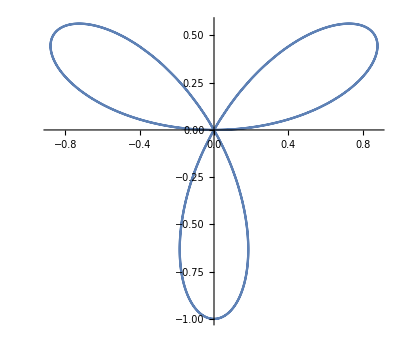

```mathematica
PolarPlot[Sin[3 θ],{θ,0,2 Pi}]
```

### Problem 1.3

Plot numerator and denominator on the interval [0,π].

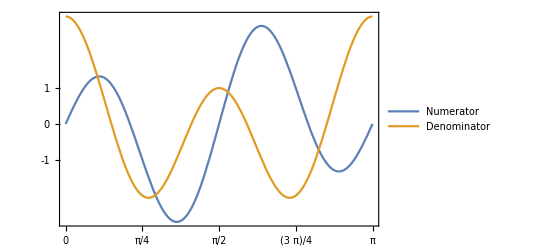

```mathematica
Plot[{3 Cos[3 θ] Sin[θ]+Sin[3 θ] Cos[θ],3 Cos[3 θ] Cos[θ]-Sin[3 θ] Sin[θ]},{θ,0,Pi},PlotLegends->{"Numerator","Denominator"},Frame->True,FrameTicks->{{{-1,0,1},None},{{0,Pi/4,Pi/2,3 Pi/4,Pi},None}}]
```

Select θ={0,0.659,π/2,2.48,π}.

```mathematica
angles={0.659,Pi/2,2.48,Pi}
```

{0.659,π/2,2.48,π}

Functions for x and y coordinates given x(r,θ)=r cos(θ) and y(r,θ)=r sin(θ).

```mathematica
xCoordinate[θ_]:=Sin[3 θ] Cos[θ];
yCoordinate[θ_]:=Sin[3 θ] Sin[θ];
```

Calculate the coordinates of the four θ values.

```mathematica
xCoordinate[angles]
yCoordinate[angles]
```

{0.726271,0,-0.722364,0}

{0.5625,-1,0.562476,0}

### Problem 1.5

```mathematica
slope[θ_]:=(3 Cos[θ] Sin[θ]+Sin[3 θ]Cos[θ])/(3 Cos[3 θ] Cos[θ]-Sin[3 θ] Sin[θ])
```

```mathematica
slope[Pi/6]
```

-(5 √3)/2

```mathematica
slope[5 Pi/6]
```

(5 √3)/2

```mathematica
slope[3 Pi/2]
```

0

### Problem 1.6

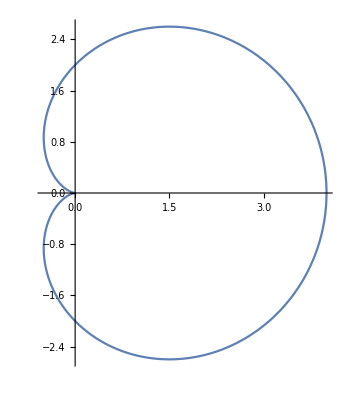

```mathematica
PolarPlot[2 (1+Cos[θ]),{θ,0,2 Pi}]
```

```mathematica
D[2 Sin[θ]+Sin[2 θ],θ]
```

2 Cos[θ]+2 Cos[2 θ]

```mathematica
Solve[2 Cos[θ]+2 Cos[2 θ]==0,θ]
```

{{θ→ConditionalExpression[-π/3+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[π/3+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

```mathematica
numerator=Union[Table[-Pi/3+2 Pi n,{n,{0,1,2,3,4,5,6}}],Table[Pi/3+2 Pi n,{n,{0,1,2,3,4,5,6}}],Table[Pi+2 Pi n,{n,{0,1,2,3,4,5,6}}]]
```

{-π/3,π/3,π,(5 π)/3,(7 π)/3,3 π,(11 π)/3,(13 π)/3,5 π,(17 π)/3,(19 π)/3,7 π,(23 π)/3,(25 π)/3,9 π,(29 π)/3,(31 π)/3,11 π,(35 π)/3,(37 π)/3,13 π}

```mathematica
D[2 Cos[θ]+2 Cos[θ]^2,θ]
```

-2 Sin[θ]-4 Cos[θ] Sin[θ]

```mathematica
Solve[-2 Sin[θ]-4 Cos[θ] Sin[θ]==0,θ]
```

{{θ→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[-(2 π)/3+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[(2 π)/3+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

```mathematica
denominator=Union[Table[2 Pi n,{n,{0,1,2,3,4,5,6}}],Table[-(2 Pi/3)+2 Pi n,{n,{0,1,2,3,4,5,6}}],Table[(2 Pi/3)+2 Pi n,{n,{0,1,2,3,4,5,6}}],Table[Pi+2 Pi n,{n,{0,1,2,3,4,5,6}}]]
```

{0,-(2 π)/3,(2 π)/3,π,(4 π)/3,2 π,(8 π)/3,3 π,(10 π)/3,4 π,(14 π)/3,5 π,(16 π)/3,6 π,(20 π)/3,7 π,(22 π)/3,8 π,(26 π)/3,9 π,(28 π)/3,10 π,(32 π)/3,11 π,(34 π)/3,12 π,(38 π)/3,13 π}

```mathematica
Complement[numerator,denominator]
```

{-π/3,π/3,(5 π)/3,(7 π)/3,(11 π)/3,(13 π)/3,(17 π)/3,(19 π)/3,(23 π)/3,(25 π)/3,(29 π)/3,(31 π)/3,(35 π)/3,(37 π)/3}

Choose θ=π/3.

```mathematica
(*x coordinate*)
(2+2 Cos[Pi/3]) Cos[Pi/3]
```

3/2

```mathematica
(*y coordinate*)
(2+2 Cos[Pi/3]) Sin[Pi/3]
```

(3 √3)/2

## 2. Integrals of polar coordinate functions

### Problem 2.2

```mathematica
PolarPlot[Sin[3 θ],{θ,0,2 Pi}]
```

-Graphics-

```mathematica
Integrate[(1/2) (Sin[3 θ])^2,{θ,0,Pi/3}]
```

π/12

### Problem 2.3

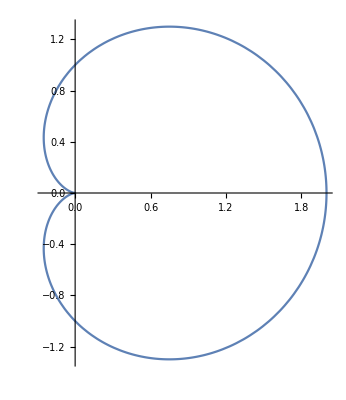

```mathematica
PolarPlot[1+Cos[θ],{θ,0,2 Pi}]
```

```mathematica
Integrate[(1/2) (1+Cos[θ])^2,{θ,0,2 Pi}]
```

(3 π)/2

### Problem 2.5

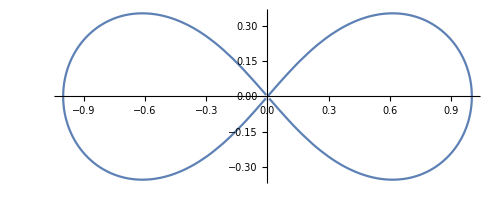

```mathematica
PolarPlot[Sqrt[Cos[2 θ]],{θ,0,2 Pi}]
```

### Problem 2.6

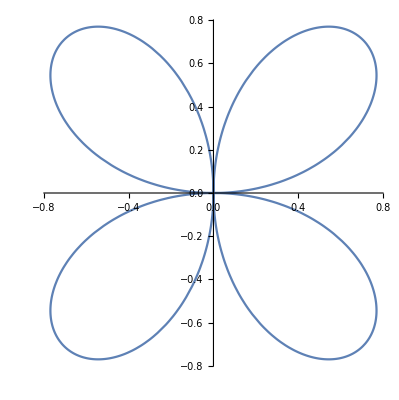

```mathematica
PolarPlot[Sin[2 θ],{θ,0,2 Pi}]
```

### Problem 2.7

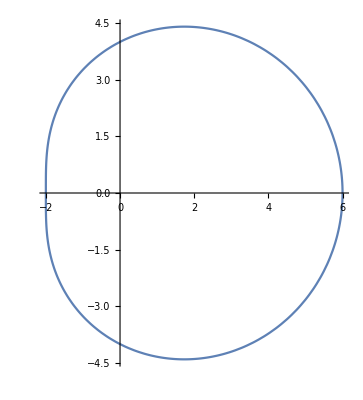

```mathematica
PolarPlot[4+2 Cos[θ],{θ,0,2 Pi}]
```

### Problem 2.8

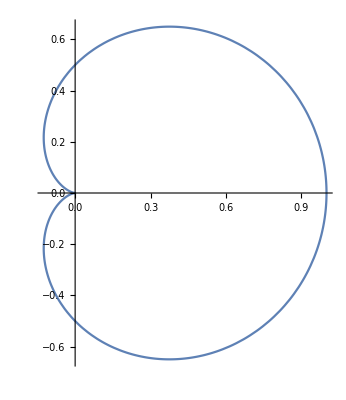

```mathematica
PolarPlot[Cos[θ/2]^2,{θ,0,2 Pi}]
```

### Problem 2.9

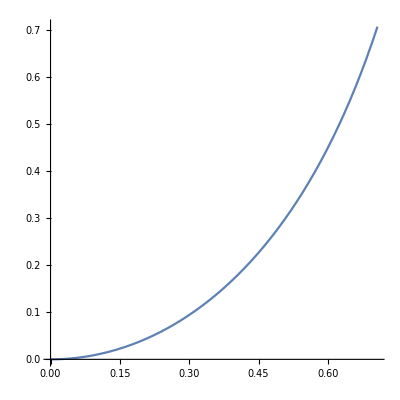

```mathematica
PolarPlot[Tan[θ],{θ,0,Pi/4}]
```

The are described by the rectangular conversion of the problem, which is not the area required.

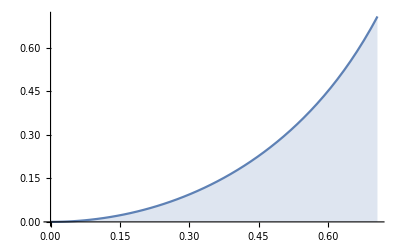

```mathematica
Plot[√(x^4/(1-x^2)),{x,0,(√2)/2},Filling->Axis]
```

The area described by the problem.

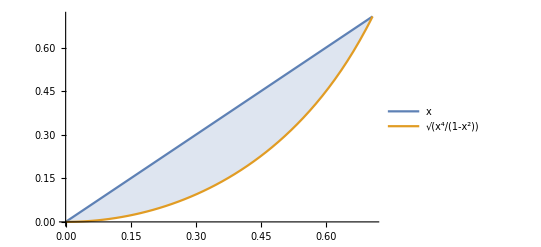

```mathematica
Plot[{x,√(x^4/(1-x^2))},{x,0,(√2)/2},PlotLegends->"Expressions",Filling->{1->{2}}]
```

The area under the curve y=x on the interval is 1/4.

```mathematica
1/4-∫_0^((√2)/2) √(x^4/(1-x^2))ⅆx//N
```

0.107301